```mathematica
Get["/Users/austingottfredson/Documents/Macbook/School/20 Fall/Dark Matter/dlNdlxEW.m"];
```

Define dN/dE that gets the flux of photons given the mass of dark matter (mdm) and ratio x (x=E/mdm)

```mathematica
dnde[mdm_,x_]:=10^(dlNdlxIEW["b"->"γ"][mdm,Log[10,x]])/(Log[10]);
specfile[mdm_]:=With[{i:=10^xp},Table[{i*mdm,dnde[mdm,i]},{xp,-7,0,.2}]];
```

i represents the variable x such that E=i*mdm

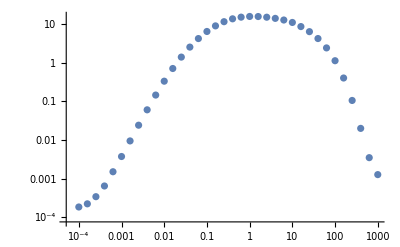

```mathematica
ListLogLogPlot[specfile[1000]]
```

Export[NotebookDirectory[] <> "specfile.txt", specfile[1000], "Table"]

/Users/austingottfredson/Indirect-Dark-Matter-Detection/specfile.txt

```mathematica
NIntegrate[dnde[1000,energy/1000],{energy,8.891,11.856}]
```

32.3829

```mathematica
eflux = {{1.25653704*10^-07},{1.90156488*10^-08},{9.51497425*10^-08},{4.11077354*10^-08},{7.15624137*10^-08},{2.37222464*10^-08},{2.29813467*10^-08},{6.25958284*10^-08},{3.69897844*10^-08},{4.41885642*10^-08},{4.87816865*10^-08},{1.4818582*10^-07},{7.81253613*10^-08},{1.57606502*10^-07},{1.50424922*10^-07},{4.13623209*10^-07},{2.35642613*10^-07},{3.15606961*10^-07},{4.22753574*10^-07},{5.678504*10^-07},{7.60294405*10^-07},{1.02597582*10^-06},{1.36382399*10^-06},{1.86842211*10^-06}};
```

```mathematica
espec = Table[NIntegrate[dnde[1000, energy/1000],{energy,emins,emaxs}]
```